```mathematica
Clear[x,y,f,g]
```

```mathematica
(* Task 2 *)
```

```mathematica
f[x_]:=E^x;
g[x_]:=1+x+x^2/2+x^3/6;
```

```mathematica
f[0.1]
```

1.10517

```mathematica
g[0.1]
```

1.10517

```mathematica
a=f[0.1]-g[0.1]
```

4.25141×10^-6

```mathematica
b=a/g[0.1]
```

3.84685×10^-6

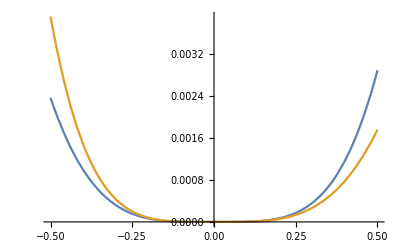

```mathematica
Plot[{f[x]-g[x],(f[x]-g[x])/g[x]},{x,-0.5,0.5}]
```

```mathematica
(* End *)
```

```mathematica
(√2)^2
```

2

```mathematica
N[(2^(1/2))^2,50]
```

2.

```mathematica
Clear[a,b,c]
```

```mathematica
a=0.456 10^-2;
b=0.123 10^0;
c=0.128 10^0;
```

```mathematica
N[a+(b+c),20]
```

0.25556

```mathematica
N[(a+b)+c,20]
```

0.25556

```mathematica
N[1/7]
```

```mathematica
0.14285714285714285
```

```mathematica
(* Task 3 *)
Clear[p,q]
```

```mathematica
p[x_]:=(x-2)^9;
```

```mathematica
q[x_]=Expand[p[x]];
```

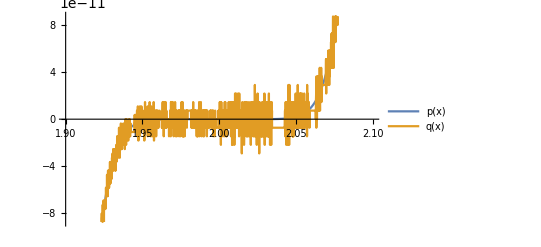

```mathematica
Plot[{p[x],q[x]},{x,1.9,2.1},PlotLegends->"Expressions"]
```

```mathematica
(* End *)
```